```mathematica
SNRList={7.11837,-7.06605,-6.70151,-6.76575,-6.87819,-6.93642,6.67535,-6.37763,7.17585,6.45762,6.56866,6.59043,-6.54153,6.63598,7.3186,7.18399,-6.73095,6.58112,-7.62746,-6.37708,7.35374,-7.44496,-6.70068,6.5212,-7.0373,6.97241,6.98097,6.67664,-7.12998,6.39625,7.2859}
List1={12863,12965,13216,13752,14695,14882,14960,14994,15433,15704,15876,15956,16044,16066,16081,16125,16154,16201,16315,16336,16413,16463,16561,16660,16664,16720,17060,17275,17445,17792,18104}
List2={478.099,599.759,611.991,627.845,388.261,556.565,506.321,595.277,615.697,574.013,37.4368,625.29,644.127,377.336,501.017,455.761,278.817,256.395,529.124,459.445,27.3333,215.637,545.824,44.5324,541.832,34.3478,620.421,421.639,554.585,63.3276,644.776}
List3=300+300*{-0.8181208135,0.4304156307,0.6901330266,-0.7679659202,-0.8957978833,0.5233126353,0.4244257393,-0.4772572288,0.4092539863,0.3376558503,-0.5125686769,-0.8068992844,0.8443918868,0.204503569,0.8386352048,0.9094448043,0.5150859474,-0.5223405155,-0.5309824637,0.08096124055,-0.8652510128,0.6920494457,0.7693123658,0.4971087488,0.6926818845,0.4800155865,0.6049877447,0.5811038631,-0.3143245116,0.6992756731,-0.8817642362}
```

{7.11837,-7.06605,-6.70151,-6.76575,-6.87819,-6.93642,6.67535,-6.37763,7.17585,6.45762,6.56866,6.59043,-6.54153,6.63598,7.3186,7.18399,-6.73095,6.58112,-7.62746,-6.37708,7.35374,-7.44496,-6.70068,6.5212,-7.0373,6.97241,6.98097,6.67664,-7.12998,6.39625,7.2859}

{12863,12965,13216,13752,14695,14882,14960,14994,15433,15704,15876,15956,16044,16066,16081,16125,16154,16201,16315,16336,16413,16463,16561,16660,16664,16720,17060,17275,17445,17792,18104}

{478.099,599.759,611.991,627.845,388.261,556.565,506.321,595.277,615.697,574.013,37.4368,625.29,644.127,377.336,501.017,455.761,278.817,256.395,529.124,459.445,27.3333,215.637,545.824,44.5324,541.832,34.3478,620.421,421.639,554.585,63.3276,644.776}

{54.5638,429.125,507.04,69.6102,31.2606,456.994,427.328,156.823,422.776,401.297,146.229,57.9302,553.318,361.351,551.591,572.833,454.526,143.298,140.705,324.288,40.4247,507.615,530.794,449.133,507.805,444.005,481.496,474.331,205.703,509.783,35.4707}

```mathematica
PlotColoredPoints[xList_,yList_,colorList_,xScale_:{Automatic,Automatic},yScale_:{Automatic,Automatic},imageSize_:400,aspectRatio_:Automatic]:=Module[{colorFunction,points},colorFunction=ColorData["Rainbow"];
points=MapThread[{colorFunction[Rescale[#3,{0,650}]],PointSize[0.02],Point[{#1,#2}]}&,{xList,yList,colorList}];
Legended[Graphics[points,Axes->True,AxesOrigin->{xScale[[1]],yScale[[1]]},PlotRange->{xScale,yScale},ImageSize->imageSize,AspectRatio->aspectRatio],BarLegend[{"Rainbow",{0,650}},LegendLabel->"Value"]]]
```

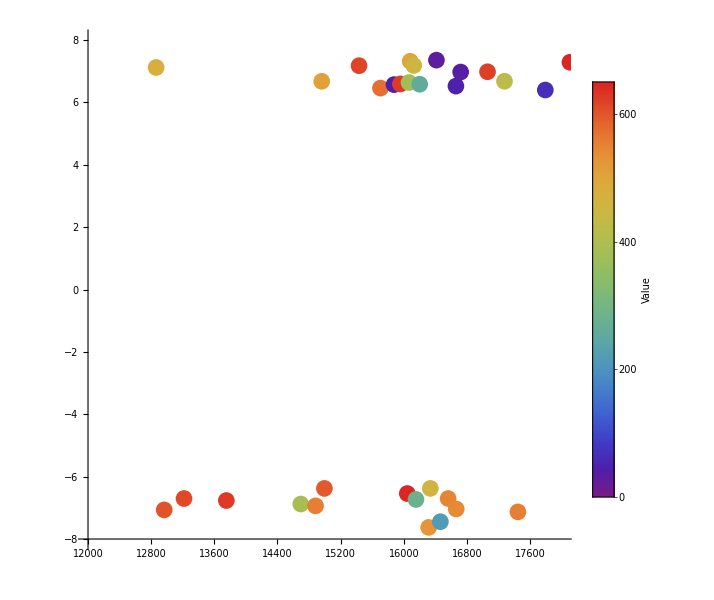

```mathematica
PlotColoredPoints[List1,SNRList,List2,{12000,18000},{-8,8},600,1]
```

```mathematica
PlotColoredPoints2[xList_,yList_,colorList_,xScale_:{Automatic,Automatic},yScale_:{Automatic,Automatic},imageSize_:400,aspectRatio_:Automatic]:=Module[{colorFunction,points},colorFunction=ColorData["Rainbow"];
points=MapThread[{colorFunction[Rescale[#3,{0,650}]],PointSize[0.02],Point[{#1,#2}]}&,{xList,yList,colorList}];
Legended[Graphics[points,Axes->True,AxesOrigin->{xScale[[1]],yScale[[1]]},PlotRange->{xScale,yScale},ImageSize->imageSize,AspectRatio->aspectRatio],BarLegend[{"Rainbow",{-1,1}},LegendLabel->"Value"]]]
```

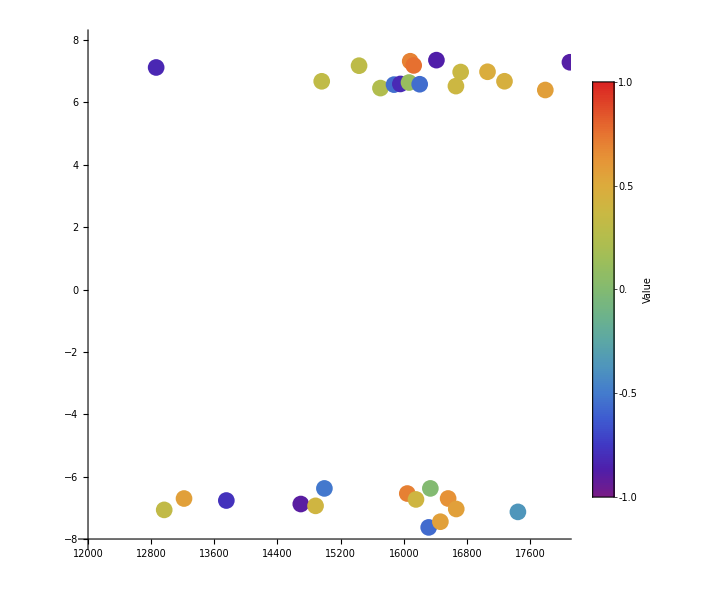

```mathematica
PlotColoredPoints2[List1,SNRList,List3,{12000,18000},{-8,8},600,1]
```